# Euler-Lagrange solver examples

## Functions

A few helper functions for generating example data and looking at the algorithm’s output. The code in this notebook depends on ELSolver.nb.

Many of the examples will be simulated using NDSolve. This function plots the system’s behaviour, showing the training and validation regions.

```mathematica
systemPlot[vars_,solution_,tTrain_,tMax_]:=Show[
Plot[(#[t]&/@vars)/.solution⟦1⟧,{t,tTrain,tMax},PlotStyle->Thickness[0.003]],
Plot[(#[t]&/@vars)/.solution⟦1⟧,{t,0,tTrain},PlotStyle->Thickness[0.01]],
PlotRange->All,Frame->True,AxesOrigin->{tTrain,0}
]
```

Generates trajectory data in the form required by the optimiser from NDSolve solutions.

```mathematica
dataFromSol[vars_,sol_,tTrain_,tStep_]:=Flatten[
(With[{θ=#[t]/.sol⟦1⟧},
{#->θ,
symbolAppend[#,"d"]->D[θ,t],
symbolAppend[#,"dd"]->D[θ,{t,2}]}]/.t->Range[0,tTrain,tStep])&/@vars,
1
]
```

Compares the discovered Lagrangian’s predictions with the system’s true behaviour.

```mathematica
predictionPlot[vars_,sol_,prediction_,tTrain_,tMax_,tStep_]:=
Show[
ListPlot[Table[{t,#[t]/.sol⟦1⟧},{t,0,tTrain,tStep}],PlotMarkers->{Graphics[{Blue,Thickness[0.2],Circle[]}],0.07}],
ListPlot[Table[{t,#[t]/.sol⟦1⟧},{t,tTrain,tMax,3tStep}],PlotStyle->{Red,PointSize[0.009]}],
Plot[#[t]/.prediction⟦1⟧,{t,tTrain ,tMax},PlotStyle->Red],
PlotRange->{{0,tMax},All},Frame->True,AxesOrigin->{tTrain,0},ImageSize->900,AspectRatio->1/6
]&/@vars
```

A function for viewing the results of a search run over trimmed polynomial models.

```mathematica
showTPResults[vars_,sol_,results_,tTrain_,tMax_,tStep_]:=TableForm[
{"maxOrder"/.#,
"trimOrder"/.#,
"steps"/.#,
"bestScore"/.#,
"inSamplePredictionError"/.#,
Show[
predictionPlot[vars,sol⟦1⟧,("predictions"/.#),tTrain,tMax,tStep],
ImageSize->160,AspectRatio->1/4
]}&/@results,
TableHeadings->{None,{"max order","trim order","iterations","score","in sample\nerror","prediction"}}]
```

Plots the prediction of the given model against the solution of the equation with the given initial conditions. Used to see if the solution that the search finds generalises to other initial conditions.

```mathematica
generalisationPlot[eq_,initGen_,params_,vars_,bestL_,tMax_]:=Module[{solGen},
solGen=NDSolve[Join[eq,initGen]/.params,vars,{t,0,tMax}];
Show[
Plot[(#/.solGen⟦1⟧)[t],{t,0,tMax}],
Plot[Evaluate[(#/.solveEL[vars,"model"/.bestL,initGen,0,tMax]⟦1⟧)[t]],{t,0,tMax},PlotStyle->{Red,Dashing[0.02]}]
]&/@vars
]
```

```mathematica
generalisationError[initTest_,eq_,params_,vars_,bestL_,tTrain_,tMax_]:=Module[{realTr,solTr},
realTr=NDSolve[Join[eq,initTest]/.params,vars,{t,0,tMax}];
solTr=solveEL[vars,"model"/.bestL,initTest,0,tMax];
NIntegrate[Plus@@(((#/.realTr⟦1⟧)[t]-(#/.solTr⟦1⟧)[t])^2&/@vars),{t,tTrain,tMax}]]
```

## Single trajectory examples

### Simple harmonic oscillator (1DOF)

```mathematica
vars={x1};
eq={m1 x1''[t]==-k1  x1[t]};
params={m1->0.5,k1->0.25};
init={x1[0]==1,x1'[0]==0};
tTrain=10;
tMax=30;
tStep=0.1;
```

```mathematica
sol=NDSolve[Join[eq,init]/.params,vars,{t,0,tMax}];
```

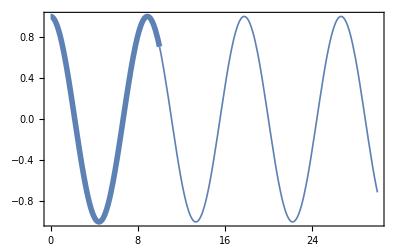

```mathematica
systemPlot[vars,sol,tTrain,tMax]
```

```mathematica
p=dataFromSol[vars,sol,tTrain,tStep];
```

```mathematica
opt=findTPLagrangian[vars,{p},{init},0.1,tTrain,tMax,tStep];//AbsoluteTiming
```

{0.150503,Null}

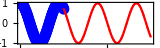
max order | trim order | iterations | score | in sample
error | prediction
2 | 2 | 230 | -18.3197 | 7.01301×10^-11 | -Graphics-

```mathematica
showTPResults[vars,sol,opt,tTrain,tMax,tStep]
```

```mathematica
bestL=pickBestTPLagrangian[opt,0.1]
```

{steps→230,bestScore→-18.3197,solution→{c1→0.907353,c2→-2.89809×10^-7,c3→-0.453677},model→-2.89809×10^-7 x1-0.453677 x1^2+0.907353 x1dot^2,inSamplePredictionError→7.01301×10^-11,predictions→{{{x1→InterpolatingFunction[{{0., 30.}}, <>]}}},trimOrder→2,maxOrder→2}

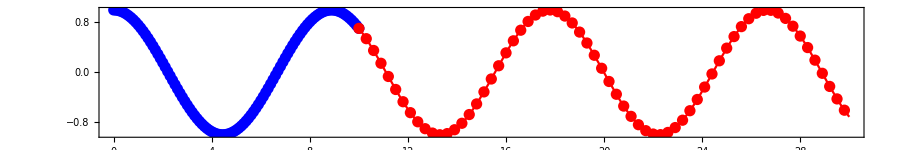

```mathematica
predictionPlot[vars,sol,("predictions"/.bestL)⟦1⟧,tTrain,tMax,tStep]
```

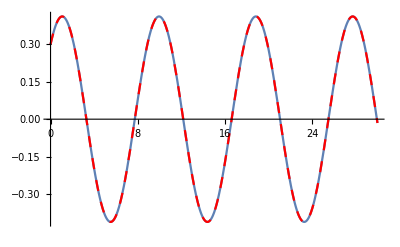

```mathematica
initGen={x1[0]==0.3,x1'[0]==0.2};
generalisationPlot[eq,initGen,params,vars,bestL,tMax]
```

### Unforced Duffing oscillator (1DOF, NL)

```mathematica
vars={x1};
eq={m1 x1''[t]==-k1  x1[t]-k2 x1[t]^3};
params={m1->1.0,k1->1.5,k2->-1.4};
init={x1[0]==1,x1'[0]==0};
tTrain=10;
tMax=30;
tStep=0.1;
```

```mathematica
sol=NDSolve[Join[eq,init]/.params,vars,{t,0,tMax}];
```

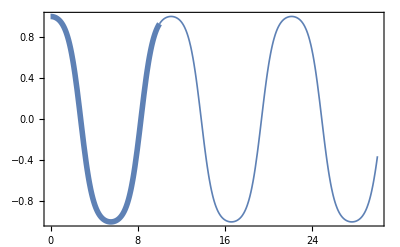

```mathematica
systemPlot[vars,sol,tTrain,tMax]
```

```mathematica
p=dataFromSol[vars,sol,tTrain,tStep];
```

```mathematica
nd=NotebookDirectory[];
Export[nd<>"../data/mma_duffing.csv",Transpose[{x1,x1d}/.p]];
```

```mathematica
opt=findTPLagrangian[vars,{p},{init},0.1,tTrain,tMax,tStep];//AbsoluteTiming
```

{4.54894,Null}

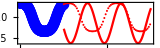
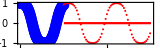
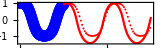
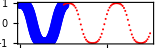
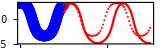
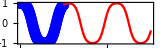
max order | trim order | iterations | score | in sample
error | prediction
2 | 2 | 140 | -0.970264 | 102.282 | -Graphics-
2 | 3 | 240 | -1.05353 | 59.7109 | -Graphics-
2 | 4 | 280 | -1.64747 | 11.6865 | -Graphics-
3 | 3 | 500 | -1.06177 | 7.93062610880025×10^403 | -Graphics-
3 | 4 | 710 | -1.68827 | 35.944 | -Graphics-
3 | 5 | 1310 | -1.90519 | 3.21557×10^144 | -Graphics-
4 | 4 | 2160 | -22.1127 | 2.69179×10^-8 | -Graphics-

```mathematica
showTPResults[vars,sol,opt,tTrain,tMax,tStep]
```

```mathematica
bestL=pickBestTPLagrangian[opt,0.1]
```

{steps→2160,bestScore→-22.1127,solution→{c1→0.201112,c2→4.96673×10^-9,c3→4.83529×10^-7,c4→-4.83699×10^-8,c5→-1.53147×10^-7,c6→2.3777×10^-8,c7→-0.30167,c8→1.77706×10^-6,c9→1.91497×10^-8,c10→0.140779},model→-4.83699×10^-8 x1-0.30167 x1^2+1.91497×10^-8 x1^3+0.140779 x1^4+0.201112 x1dot^2-1.53147×10^-7 x1 x1dot^2+1.77706×10^-6 x1^2 x1dot^2+4.96673×10^-9 x1dot^3+2.3777×10^-8 x1 x1dot^3+4.83529×10^-7 x1dot^4,inSamplePredictionError→2.69179×10^-8,predictions→{{{x1→InterpolatingFunction[{{0., 30.}}, <>]}}},trimOrder→4,maxOrder→4}

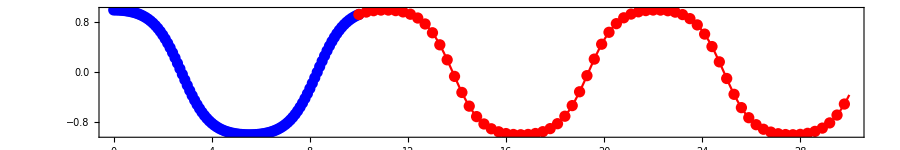

```mathematica
predictionPlot[vars,sol,("predictions"/.bestL)⟦1⟧,tTrain,tMax,tStep]
```

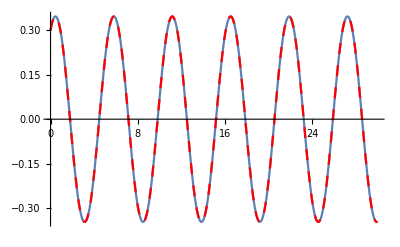

```mathematica
initGen={x1[0]==0.3,x1'[0]==0.2};
generalisationPlot[eq,initGen,params,vars,bestL,tMax]
```

```mathematica
Chop["model"/.bestL,10^-5]
```

-0.30167 x1^2+0.140779 x1^4+0.201112 x1dot^2

The Lagrangian as would be written by a human:

1/2(ẋ)^2-1/2 3/2 x^2+1/4 1.4 x^4

Comparing these coefficients, after scaling the velocity term to match the hand written value.

```mathematica
0.5/0.201112295794452{-0.30167009526300415 ,0.14077933537511697,0.201112295794452 }
```

{-0.750004,0.350002,0.5}

We see that the are correct up to the 6th decimal place.

### Simple pendulum (1DOF, NL)

```mathematica
vars={x1};
eq={m1 x1''[t]==-k1 Sin[ x1[t]]};
params={m1->0.5,k1->2};
init={x1[0]==1.3 π/2,x1'[0]==0};
tTrain=10;
tMax=30;
tStep=0.1;
```

```mathematica
sol=NDSolve[Join[eq,init]/.params,vars,{t,0,tMax}];
```

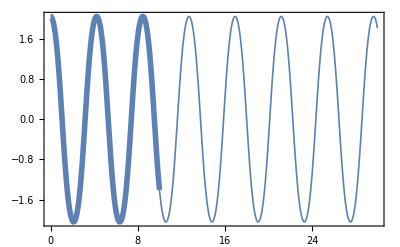

```mathematica
systemPlot[vars,sol,tTrain,tMax]
```

```mathematica
p=dataFromSol[vars,sol,tTrain,tStep];
```

```mathematica
nd=NotebookDirectory[];
Export[nd<>"../data/mma_pendulum.csv",Transpose[{x1,x1d}/.p]];
```

```mathematica
opt=findTPLagrangian[vars,{p},{init},0.1,tTrain,tMax,tStep];//AbsoluteTiming
```

{0.500633,Null}

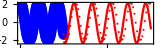
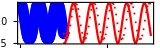
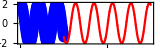
max order | trim order | iterations | score | in sample
error | prediction
2 | 2 | 170 | -1.28186 | 22.6922 | -Graphics-
2 | 3 | 290 | -1.35849 | 35.8441 | -Graphics-
2 | 4 | 480 | -5.42253 | 0.00162823 | -Graphics-

```mathematica
showTPResults[vars,sol,opt,tTrain,tMax,tStep]
```

```mathematica
bestL=pickBestTPLagrangian[opt,0.1]
```

{steps→480,bestScore→-5.42253,solution→{c1→-0.030498,c2→0.000495936,c3→-0.0000303714,c4→0.085588,c5→-0.00411355},model→0.000495936 x1+0.085588 x1^2-0.030498 x1dot^2-0.0000303714 x1 x1dot^2-0.00411355 x1^2 x1dot^2,inSamplePredictionError→0.00162823,predictions→{{{x1→InterpolatingFunction[{{0., 30.}}, <>]}}},trimOrder→4,maxOrder→2}

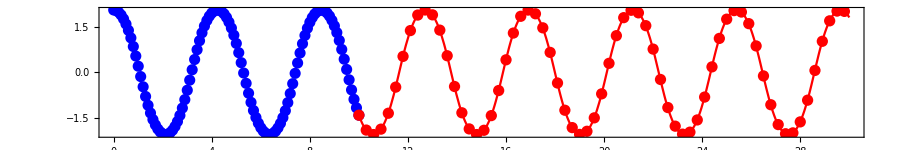

```mathematica
predictionPlot[vars,sol,("predictions"/.bestL)⟦1⟧,tTrain,tMax,tStep]
```

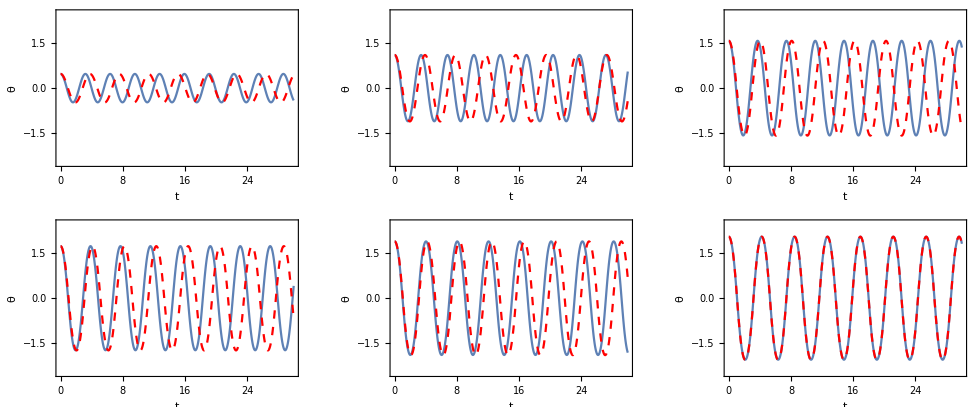

```mathematica
initGens={x1[0]==# π/2,x1'[0]==0}&/@{0.3,0.7,1.0,1.1,1.2,1.3};
initPlot=GraphicsGrid[Partition[Show[#,Frame->True,PlotRange->{All,{-2.5,2.5}},ImageSize->300,FrameLabel->{"t","θ"},LabelStyle->{FontSize->17}]&/@Flatten[generalisationPlot[eq,#,params,vars,bestL,tMax]&/@initGens],3]]
```

```mathematica
Export[NotebookDirectory[]<>"init.pdf", initPlot];
```

```mathematica
100("model"/.bestL)//Expand
```

0.0495936 x1+8.5588 x1^2-3.0498 x1dot^2-0.00303714 x1 x1dot^2-0.411355 x1^2 x1dot^2

```mathematica
testModel=0.08558799143046138 x1^2-0.030497979542467253 x1dot^2-0.004113550744514775 x1^2 x1dot^2
```

0.085588 x1^2-0.030498 x1dot^2-0.00411355 x1^2 x1dot^2

```mathematica
testModel//Simplify
```

-0.030498 x1dot^2+x1^2 (0.085588-0.00411355 x1dot^2)

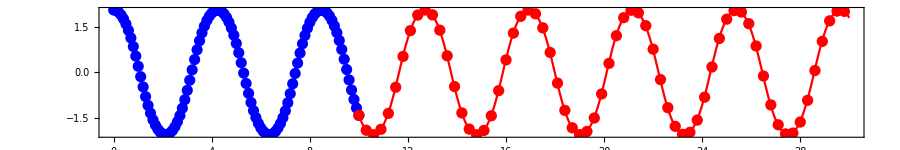

{{x1→InterpolatingFunction[{{0., 30.}}, <>]}}

```mathematica
predictionPlot[vars,sol,solveEL[vars,testModel,init,0,30],tTrain,tMax,tStep]
```

```mathematica
ge={#,generalisationError[{x1[0]==# π/2,x1'[0]==0},eq,params,vars,bestL,tTrain,tMax]}&/@Range[0.0,1.9,0.02];
```

$Aborted

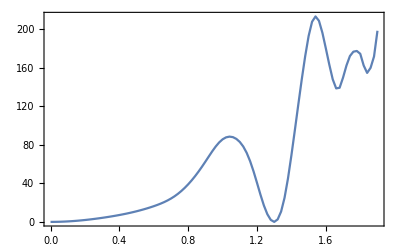

```mathematica
pendulumSingleGE=ListPlot[ge,Joined->True,Frame->True]
```

### Coupled harmonic oscillators (2DOF)

```mathematica
vars={x1,x2};
eq={
m1 x1''[t]==-k1 (l1+x1[t]) + k2 (l2+(x2[t]-x1[t])),
m2 x2''[t]==-k2(l2+(x2[t]-x1[t]))+k3 (l3-x2[t])
};
params={m1->0.5,m2->0.9,k1->1,k2->2,k3->1,l1->1,l2->1,l3->1};
init={x1[0]==0,x2[0]==1.1,x1'[0]==0,x2'[0]==0};
tMax=30;
tTrain=10;
tStep=0.1;
```

```mathematica
sol=NDSolve[Join[eq,init]/.params,vars,{t,0,tMax}];
```

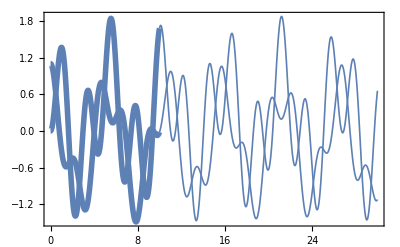

```mathematica
systemPlot[vars,sol,tTrain,tMax]
```

```mathematica
p=dataFromSol[vars,sol,tTrain,tStep];
```

```mathematica
nd=NotebookDirectory[];
Export[nd<>"../data/mma_coupled_sho.csv",Transpose[{x1,x1d}/.p]];
```

```mathematica
(*ListPlot[vars/.p]*)
```

```mathematica
opt=findTPLagrangian[vars,{p},{init},0.1,tTrain,tMax,tStep];//AbsoluteTiming
```

{1.28575,Null}

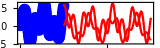
max order | trim order | iterations | score | in sample
error | prediction
2 | 2 | 1740 | -21.3434 | 1.53996×10^-11 | -Graphics-

```mathematica
showTPResults[vars,sol,opt,tTrain,tMax,tStep]
```

```mathematica
bestL=pickBestTPLagrangian[opt,0.1]
```

{steps→1740,bestScore→-21.3434,solution→{c1→-0.413791,c2→0.216882,c3→0.676649,c4→-0.351326,c5→-0.108837,c6→-0.112775,c7→-0.060737,c8→-0.108837,c9→0.268889,c10→0.286287},model→-0.060737 x1+0.286287 x1^2-0.112775 x1dot^2+0.216882 x2+0.268889 x1 x2-0.108837 x1dot x2+0.676649 x2^2-0.108837 x1 x2dot-0.351326 x1dot x2dot-0.413791 x2dot^2,inSamplePredictionError→1.53996×10^-11,predictions→{{{x1→InterpolatingFunction[{{0., 30.}}, <>],x2→InterpolatingFunction[{{0., 30.}}, <>]}}},trimOrder→2,maxOrder→2}

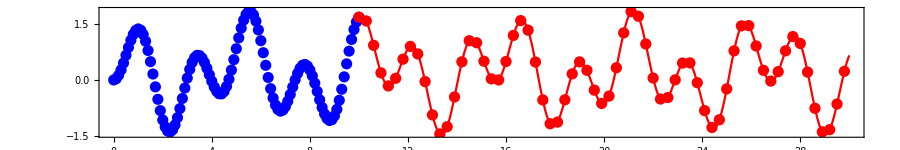
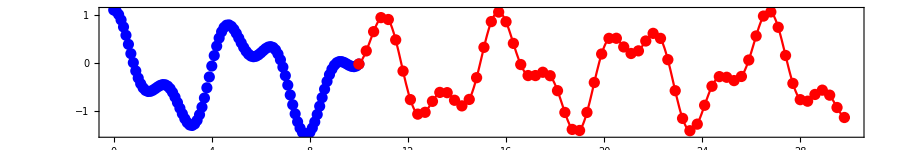

```mathematica
predictionPlot[vars,sol,("predictions"/.bestL)⟦1⟧,tTrain,tMax,tStep]
```

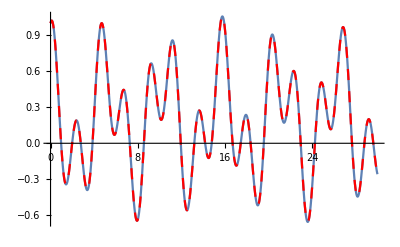
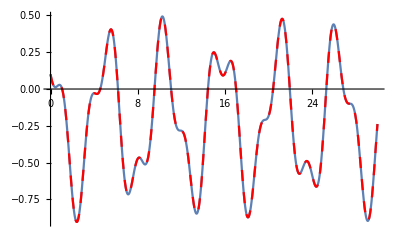

```mathematica
initGen={x1[0]==1.0,x2[0]==0.1,x1'[0]==0.4,x2'[0]==-0.4};
generalisationPlot[eq,initGen,params,vars,bestL,tMax]
```

### Coupled harmonic oscillators with noise (2 DOF, noisy)

```mathematica
vars={x1,x2};
eq={
m1 x1''[t]==-k1 (l1+x1[t]) + k2 (l2+(x2[t]-x1[t])),
m2 x2''[t]==-k2(l2+(x2[t]-x1[t]))+k3 (l3-x2[t])
};
params={m1->0.5,m2->0.9,k1->1,k2->2,k3->1,l1->1,l2->1,l3->1};
init={x1[0]==0,x2[0]==1.1,x1'[0]==0,x2'[0]==0};
tMax=30;
tTrain=10;
tStep=0.1;
```

```mathematica
sol=NDSolve[Join[eq,init]/.params,vars,{t,0,tMax}];
```

```mathematica
systemPlot[vars,sol,tTrain,tMax]
```

-Graphics-

Note that we generate the data for all time here, not just the training period.

```mathematica
pFull=dataFromSol[vars,sol,tMax,tStep];
```

And noise it up.

```mathematica
varsAndDs=Join[vars, symbolAppend[#, "d"] & /@ vars, symbolAppend[#, "dd"] & /@ vars];
```

```mathematica
pFullNoisy=# -> (RandomVariate[NormalDistribution[#, 0.1]] & /@ (# /. pFull)) & /@varsAndDs;
```

```mathematica
p=(#->Take[#/.pFullNoisy,tTrain/tStep+1])&/@varsAndDs;
```

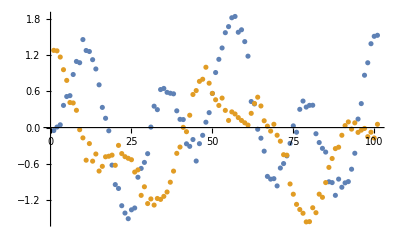

```mathematica
ListPlot[vars/.p]
```

```mathematica
opt=findTPLagrangian[vars,{p},{init},10.0,tTrain,tMax,tStep];//AbsoluteTiming
```

{0.692477,Null}

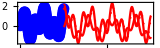
max order | trim order | iterations | score | in sample
error | prediction
2 | 2 | 1240 | -3.229 | 6.34911 | -Graphics-

```mathematica
showTPResults[vars,sol,opt,tTrain,tMax,tStep]
```

```mathematica
bestL=pickBestTPLagrangian[opt,10]
```

{steps→1240,bestScore→-3.229,solution→{c1→-0.0329154,c2→0.0121536,c3→0.0455629,c4→-0.0318848,c5→-1.,c6→-0.00738367,c7→0.00766515,c8→-0.999997,c9→0.0472473,c10→0.00947774},model→0.00766515 x1+0.00947774 x1^2-0.00738367 x1dot^2+0.0121536 x2+0.0472473 x1 x2-1. x1dot x2+0.0455629 x2^2-0.999997 x1 x2dot-0.0318848 x1dot x2dot-0.0329154 x2dot^2,inSamplePredictionError→6.34911,predictions→{{{x1→InterpolatingFunction[{{0., 30.}}, <>],x2→InterpolatingFunction[{{0., 30.}}, <>]}}},trimOrder→2,maxOrder→2}

```mathematica
<<ErrorBarPlots`
```

```mathematica
predictionPlotNoisy[vars_,sol_,prediction_,tTrain_,tMax_,tStep_, errorSize_]:=
Show[
ErrorListPlot[{#,ErrorBar[errorSize]}&/@Transpose[{Table[t,{t,0,tTrain,tStep}],#/.p}],PlotStyle->{Blue,PointSize[0.01],Thickness[0.003]}],
ErrorListPlot[Take[Drop[{#,ErrorBar[errorSize]}&/@Transpose[{Table[t,{t,0,tMax,tStep}],#/.pFullNoisy}],101],{1,200,3}],PlotStyle->{Red,PointSize[0.01],Thickness[0.003]}],
Plot[#[t]/.prediction⟦1⟧,{t,tTrain ,tMax},PlotStyle->{Red,Thickness[0.003]}],
PlotRange->{{0,tMax},All},Frame->True,AxesOrigin->{tTrain,0},ImageSize->450,AspectRatio->1/3,LabelStyle->{FontSize->12},FrameLabel->{"t",ToString[#]}
]&/@vars
```

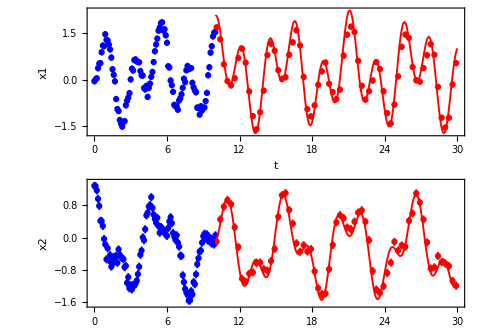

```mathematica
noisePlot=GraphicsColumn[predictionPlotNoisy[vars,sol,("predictions"/.bestL)⟦1⟧,tTrain,tMax,tStep,0.1]]
```

```mathematica
Export[NotebookDirectory[]<>"noise.pdf",noisePlot];
```

### Double pendulum (2DOF, NL)

```mathematica
vars={θ1,θ2};
eq={
(m1+m2) l1 θ1''[t]+m2 l2 θ2''[t] Cos[θ1[t]-θ2[t]]+m2 l2 θ2'[t]^2 Sin[θ1[t]-θ2[t]]+g(m1+m2)Sin[θ1[t]]==0,m2 l2 θ2''[t]+m2 l1 θ1''[t]Cos[θ1[t]-θ2[t]]-m2 l1 θ1'[t]^2 Sin[θ1[t]-θ2[t]]+m2 g Sin[θ2[t]]==0
};
params={m1->1,m2->1,l1-> 0.5,l2->0.8,g->9.8};
init={θ1[0]==1,θ2[0]==0.5,θ1'[0]==0,θ2'[0]==0};
tMax=30;
tTrain=10;
tStep=0.1;
```

```mathematica
sol=NDSolve[Join[eq,init]/.params,vars,{t,0,tMax}];
```

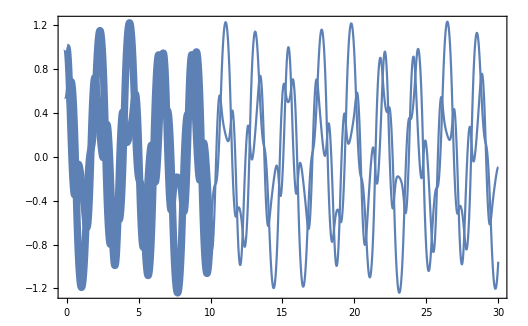

```mathematica
systemPlot[vars,sol,tTrain,tMax]
```

```mathematica
p=dataFromSol[vars,sol,tTrain,tStep];
```

```mathematica
nd=NotebookDirectory[];
Export[nd<>"../data/mma_double.csv",Transpose[vars/.p]];
```

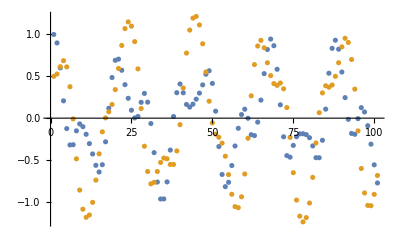

```mathematica
ListPlot[vars/.p,Joined->False]
```

```mathematica
(*opt=findTPLagrangian[vars,{p},{init},0.1,tTrain,tMax,tStep];//AbsoluteTiming*)
```

```mathematica
(*DumpSave[NotebookDirectory[]<>"pendulum.mx",opt];*)
```

```mathematica
<<(NotebookDirectory[]<>"pendulum.mx");
```

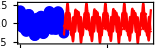
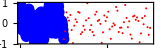
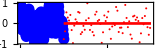
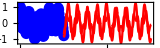
max order | trim order | iterations | score | in sample
error | prediction
2 | 2 | 2510 | -3.60431 | 59.8083 | -Graphics-
2 | 3 | 42640 | -4.53895 | 1.86293×10^54 | -Graphics-
3 | 3 | 86350 | -5.36841 | 72.7598 | -Graphics-
2 | 4 | 269470 | -9.60919 | 0.0108344 | -Graphics-

```mathematica
showTPResults[vars,sol,opt,tTrain,tMax,tStep]
```

```mathematica
bestL=pickBestTPLagrangian[opt,0.1]
```

{steps→269470,bestScore→-9.60919,solution→{c1→-0.00409321,c2→-0.000108383,c3→-4.0205×10^-6,c4→0.0427472,c5→-0.000331616,c6→-0.00523362,c7→-1.70607×10^-7,c8→0.047155,c9→-0.000025131,c10→4.55194×10^-7,c11→0.143175,c12→0.00208584,c13→-0.00312841,c14→-5.83177×10^-8,c15→-1.55844×10^-6,c16→-0.0000161036,c17→-4.28552×10^-7,c18→-0.000208652,c19→-0.000294194,c20→0.047162,c21→-2.93707×10^-6,c22→0.00138642,c23→0.286332,c24→-0.00033779,c25→0.000112358,c26→-2.63267×10^-6,c27→-0.000024403,c28→6.41549×10^-7,c29→0.260658,c30→-0.00600821,c31→-0.410503,c32→-0.0000129493,c33→1.05656×10^-6,c34→-0.000400606,c35→0.0521999,c36→0.130334,c37→-0.000190888,c38→0.000846504,c39→-0.410493,c40→0.0194428,c41→0.00222518,c42→0.000031792,c43→-0.000182692},model→-0.000294194 θ1+0.0521999 θ1^2-0.00312841 θ1dot^2-0.0000129493 θ1 θ1dot^2-0.000182692 θ1^2 θ1dot^2-0.000108383 θ2+0.00138642 θ1 θ2+0.000846504 θ1^2 θ2+0.047155 θ1dot θ2+0.260658 θ1 θ1dot θ2+0.000031792 θ1^2 θ1dot θ2-0.0000161036 θ1dot^2 θ2-0.000400606 θ1 θ1dot^2 θ2+0.0427472 θ2^2+0.000112358 θ1 θ2^2+0.0194428 θ1^2 θ2^2+0.143175 θ1dot θ2^2-0.410503 θ1 θ1dot θ2^2-0.000208652 θ1dot^2 θ2^2+0.047162 θ1 θ2dot+0.130334 θ1^2 θ2dot-0.00523362 θ1dot θ2dot-0.000024403 θ1 θ1dot θ2dot+0.00222518 θ1^2 θ1dot θ2dot-5.83177×10^-8 θ1dot^2 θ2dot+1.05656×10^-6 θ1 θ1dot^2 θ2dot+0.286332 θ1 θ2 θ2dot-0.410493 θ1^2 θ2 θ2dot-0.000025131 θ1dot θ2 θ2dot-0.00600821 θ1 θ1dot θ2 θ2dot-4.28552×10^-7 θ1dot^2 θ2 θ2dot-2.63267×10^-6 θ1 θ2^2 θ2dot+0.00208584 θ1dot θ2^2 θ2dot-0.00409321 θ2dot^2-2.93707×10^-6 θ1 θ2dot^2-0.000190888 θ1^2 θ2dot^2-1.70607×10^-7 θ1dot θ2dot^2+6.41549×10^-7 θ1 θ1dot θ2dot^2-1.55844×10^-6 θ1dot^2 θ2dot^2-4.0205×10^-6 θ2 θ2dot^2-0.00033779 θ1 θ2 θ2dot^2+4.55194×10^-7 θ1dot θ2 θ2dot^2-0.000331616 θ2^2 θ2dot^2,inSamplePredictionError→0.0108344,predictions→{{{θ1→InterpolatingFunction[{{0., 30.}}, <>],θ2→InterpolatingFunction[{{0., 30.}}, <>]}}},trimOrder→4,maxOrder→2}

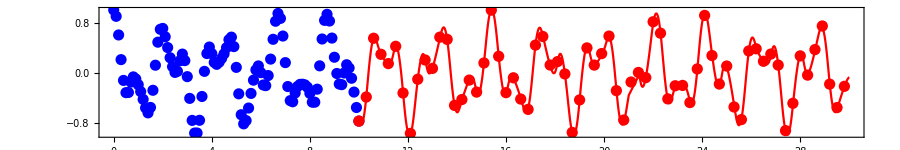
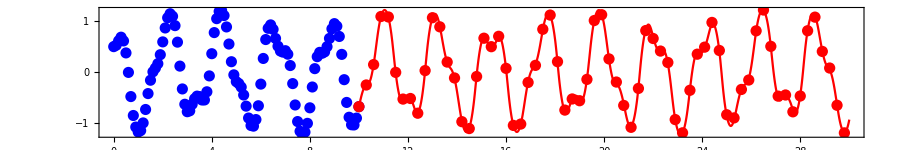

```mathematica
predictionPlot[vars,sol,("predictions"/.bestL)⟦1⟧,tTrain,tMax,tStep]
```

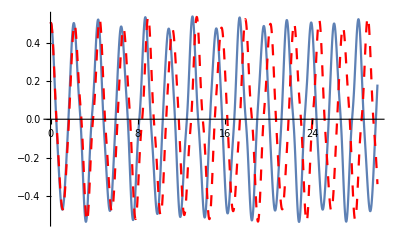
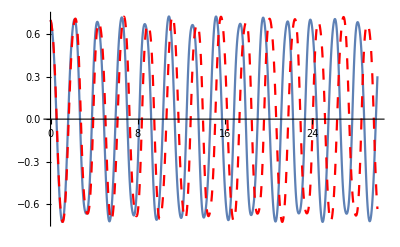

```mathematica
initGen={θ1[0]==0.5,θ2[0]==0.7,θ1'[0]==0.2,θ2'[0]==-0.2};
generalisationPlot[eq,initGen,params,vars,bestL,tMax]
```

```mathematica
ge=generalisationError[{θ1[0]==#,θ2[0]==0.2,θ1'[0]==0.0,θ2'[0]==0.0},eq,params,vars,bestL,tTrain,tMax]&/@Range[0.0,1.0,0.1]
```

{0.785337,1.10534,1.97611,3.45231,5.61492,8.68087,13.1845,19.2824,24.2205,19.9787,9.3702}

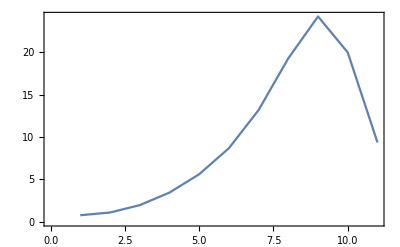

```mathematica
doubleGESingle=ListPlot[ge,Joined->True,Frame->True]
```

### Ideal Penning trap (3DOF)

```mathematica
vars={x,y,z};
eq={
m x''[t]==ωc y'[t]+1/2 ωz^2 x[t],
m y''[t]==-ωc x'[t]+1/2 ωz^2 y[t],
m z''[t]==-ωz^2 z[t]
};
params={m->0.4,ωc->1,ωz->0.5};
init={x[0]==1,y[0]==1.5,z[0]==0.5,x'[0]==0,y'[0]==0,z'[0]==0};
tMax=30;
tTrain=10;
tStep=0.1;
```

```mathematica
sol=NDSolve[Join[eq,init]/.params,vars,{t,0,tMax}];
```

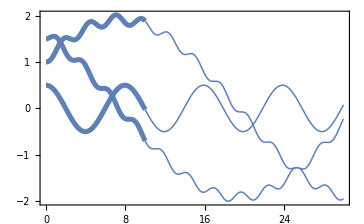

```mathematica
systemPlot[vars,sol,tTrain,tMax]
```

```mathematica
p=dataFromSol[vars,sol,tTrain,tStep];
```

```mathematica
(*ListPlot[vars/.p]*)
```

```mathematica
opt=findTPLagrangian[vars,{p},{init},0.1,tTrain,tMax,tStep];//AbsoluteTiming
```

{6.19184,Null}

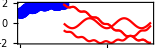
max order | trim order | iterations | score | in sample
error | prediction
2 | 2 | 5650 | -21.7284 | 5.0972×10^-11 | -Graphics-

```mathematica
showTPResults[vars,sol,opt,tTrain,tMax,tStep]
```

```mathematica
bestL=pickBestTPLagrangian[opt,0.1]
```

{steps→5650,bestScore→-21.7284,solution→{c1→0.307656,c2→1.52389×10^-8,c3→-0.192285,c4→-4.69537×10^-9,c5→0.262913,c6→0.117273,c7→2.12777×10^-8,c8→0.262913,c9→1.08294×10^-9,c10→0.0366478,c11→-2.88957×10^-8,c12→0.0553178,c13→-9.13832×10^-9,c14→-0.556775,c15→0.117273,c16→-3.16336×10^-7,c17→0.0553177,c18→-2.20826×10^-8,c19→0.0295896,c20→-1.66284×10^-8,c21→0.0366479},model→-3.16336×10^-7 x+0.0366479 x^2+0.117273 xdot^2+2.12777×10^-8 y-1.66284×10^-8 x y-0.556775 xdot y+0.0366478 y^2+0.0295896 x ydot-9.13832×10^-9 xdot ydot+0.117273 ydot^2+1.52389×10^-8 z-2.20826×10^-8 x z+0.0553178 xdot z+1.08294×10^-9 y z+0.262913 ydot z-0.192285 z^2+0.0553177 x zdot-2.88957×10^-8 xdot zdot+0.262913 y zdot-4.69537×10^-9 ydot zdot+0.307656 zdot^2,inSamplePredictionError→5.0972×10^-11,predictions→{{{x→InterpolatingFunction[{{0., 30.}}, <>],y→InterpolatingFunction[{{0., 30.}}, <>],z→InterpolatingFunction[{{0., 30.}}, <>]}}},trimOrder→2,maxOrder→2}

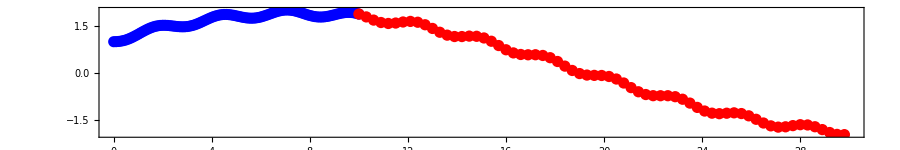
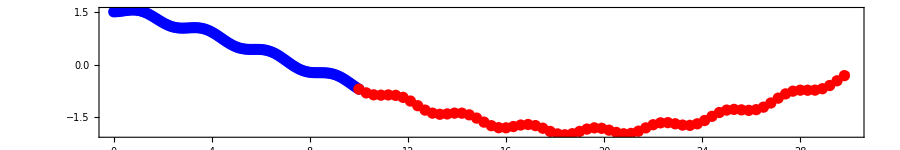
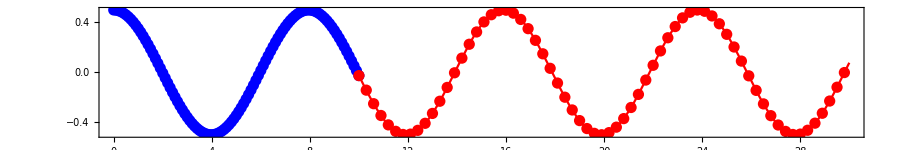

```mathematica
predictionPlot[vars,sol,("predictions"/.bestL)⟦1⟧,tTrain,tMax,tStep]
```

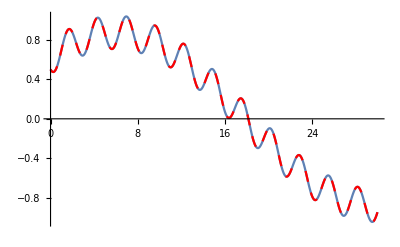
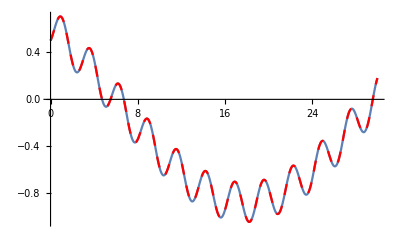
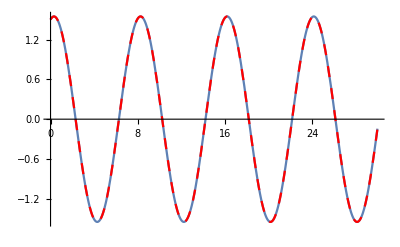

```mathematica
initGen={x[0]==0.5,y[0]==0.5,z[0]==1.5,x'[0]==-0.2,y'[0]==0.2,z'[0]==0.3};
generalisationPlot[eq,initGen,params,vars,bestL,tMax]
```

## Multi-trajectory examples

### Simple pendulum (1DOF, NL)

```mathematica
vars={x1};
eq={m1 x1''[t]==-k1 Sin[ x1[t]]};
params={m1->0.5,k1->2};
init={x1[0]==# π/2,x1'[0]==0}&/@{0.7,1.0,1.1,1.2,1.3};
tTrain=10;
tMax=30;
tStep=0.1;
```

```mathematica
sol=NDSolve[Join[eq,#]/.params,vars,{t,0,tMax}]&/@init;
```

```mathematica
pl=dataFromSol[vars,#,tTrain,tStep]&/@sol;
```

```mathematica
opt=findTPLagrangian[vars,pl,init,0.1,tTrain,tMax,tStep];//AbsoluteTiming
```

{7.07266,Null}

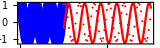
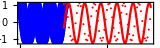
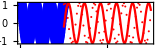
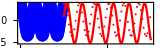
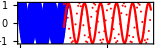
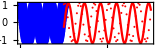
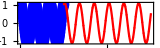
max order | trim order | iterations | score | in sample
error | prediction
2 | 2 | 140 | -9.93625 | 443.353 | -Graphics-
2 | 3 | 290 | -10.0309 | 442.574 | -Graphics-
2 | 4 | 410 | -20.9723 | 140.867 | -Graphics-
3 | 3 | 540 | -10.6749 | 235.454 | -Graphics-
3 | 4 | 1060 | -21.054 | 142.82 | -Graphics-
3 | 5 | 2740 | -21.2817 | 144.312 | -Graphics-
4 | 4 | 3270 | -49.6557 | 0.0746623 | -Graphics-

```mathematica
showTPResults[vars,sol,opt,tTrain,tMax,tStep]
```

```mathematica
bestL=pickBestTPLagrangian[opt,0.1]
```

{steps→3270,bestScore→-49.6557,solution→{c1→0.0228026,c2→-1.69455×10^-7,c3→0.0000758166,c4→-8.90333×10^-7,c5→5.10735×10^-9,c6→-1.51828×10^-7,c7→-0.0918994,c8→0.00156244,c9→6.39887×10^-7,c10→0.00493456},model→-8.90333×10^-7 x1-0.0918994 x1^2+6.39887×10^-7 x1^3+0.00493456 x1^4+0.0228026 x1dot^2+5.10735×10^-9 x1 x1dot^2+0.00156244 x1^2 x1dot^2-1.69455×10^-7 x1dot^3-1.51828×10^-7 x1 x1dot^3+0.0000758166 x1dot^4,inSamplePredictionError→0.0746623,predictions→{{{x1→InterpolatingFunction[{{0., 30.}}, <>]}},{{x1→InterpolatingFunction[{{0., 30.}}, <>]}},{{x1→InterpolatingFunction[{{0., 30.}}, <>]}},{{x1→InterpolatingFunction[{{0., 30.}}, <>]}},{{x1→InterpolatingFunction[{{0., 30.}}, <>]}}},trimOrder→4,maxOrder→4}

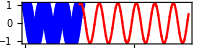
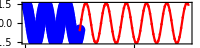
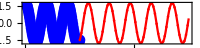
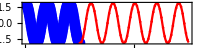
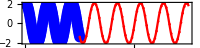

```mathematica
MapThread[Show[predictionPlot[vars,#1,#2,tTrain,tMax,tStep],ImageSize->200]&,{sol,"predictions"/.bestL}]
```

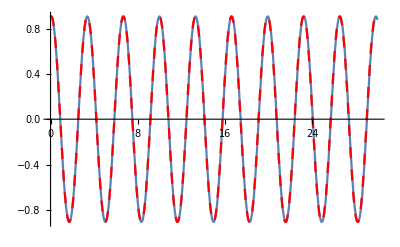

```mathematica
initGen={x1[0]==0.9,x1'[0]==0.2};
generalisationPlot[eq,initGen,params,vars,bestL,tMax]
```

```mathematica
ge={#,generalisationError[{x1[0]==# π/2,x1'[0]==0},eq,params,vars,bestL,tTrain,tMax]}&/@Range[0.0,1.9,0.02];
```

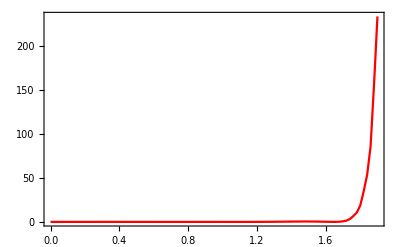

```mathematica
pendulumMultiGE=ListPlot[ge,Joined->True,Frame->True,PlotStyle->Red,PlotRange->All]
```

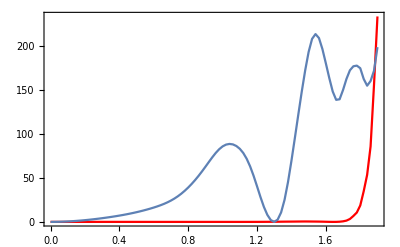

```mathematica
Show[pendulumMultiGE,pendulumSingleGE,PlotRange->All]
```

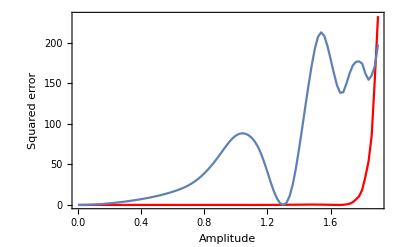

```mathematica
genPlot=Show[-Graphics-,FrameLabel->{"Amplitude","Squared error"},LabelStyle->{FontSize->15}]
```

```mathematica
Export[NotebookDirectory[]<>"gen.pdf",genPlot];
```

### Double pendulum (2DOF, NL)

```mathematica
vars={θ1,θ2};
eq={
(m1+m2) l1 θ1''[t]+m2 l2 θ2''[t] Cos[θ1[t]-θ2[t]]+m2 l2 θ2'[t]^2 Sin[θ1[t]-θ2[t]]+g(m1+m2)Sin[θ1[t]]==0,m2 l2 θ2''[t]+m2 l1 θ1''[t]Cos[θ1[t]-θ2[t]]-m2 l1 θ1'[t]^2 Sin[θ1[t]-θ2[t]]+m2 g Sin[θ2[t]]==0
};
params={m1->1,m2->1,l1-> 0.5,l2->0.8,g->9.8};
init={θ1[0]==#,θ2[0]==0.2,θ1'[0]==0,θ2'[0]==0}&/@{0.7,0.8,0.9,1.0};
tMax=30;
tTrain=10;
tStep=0.1;
```

```mathematica
sol=NDSolve[Join[eq,#]/.params,vars,{t,0,tMax}]&/@init;
```

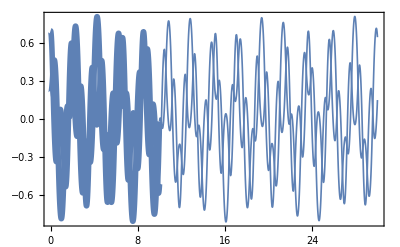
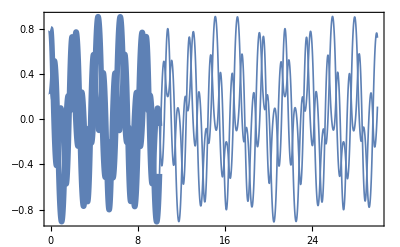
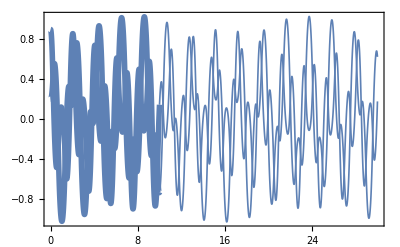
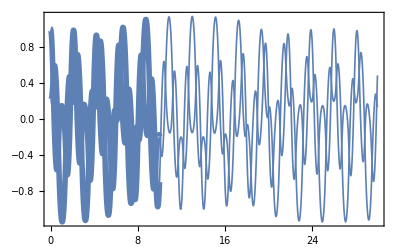

```mathematica
systemPlot[vars,#,tTrain,tMax]&/@sol
```

```mathematica
pl=dataFromSol[vars,#,tTrain,tStep]&/@sol;
```

```mathematica
opt=findTPLagrangian[vars,pl,init,0.1,tTrain,tMax,tStep];//AbsoluteTiming
```

```mathematica
(*pred=optimiseTrimmedPolynomial[vars,pl,init,tTrain,tMax,tStep,4,4]*)
```

```mathematica
showTPResults[vars,sol,opt,tTrain,tMax,tStep]
```

```mathematica
bestL=pred;(*pickBestTPLagrangian[opt,0.1]*)
```

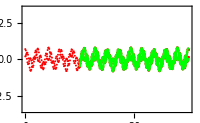
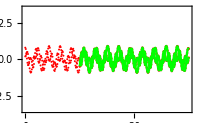
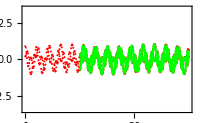
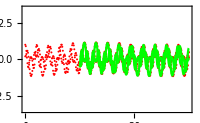

```mathematica
MapThread[Show[predictionPlot[vars,#1,#2,tTrain,tMax,tStep],ImageSize->200]&,{sol,("predictions"/.bestL)}]
```

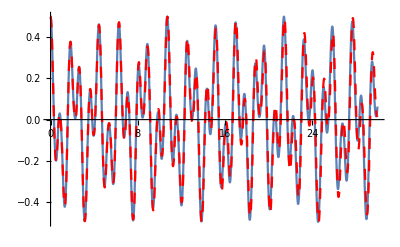
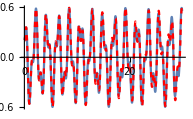

```mathematica
initGen={θ1[0]==0.5,θ2[0]==0.2,θ1'[0]==0.0,θ2'[0]==0.0};
generalisationPlot[eq,initGen,params,vars,bestL,tMax]
```

```mathematica
ge=generalisationError[{θ1[0]==#,θ2[0]==0.2,θ1'[0]==0.0,θ2'[0]==0.0},eq,params,vars,bestL,tTrain,tMax]&/@Range[0.0,1.0,0.1]
```

{0.0012352,0.000315138,0.0015647,0.0171274,0.0545476,0.0937209,0.100153,0.0328725,0.0152393,0.446946,1.88742}

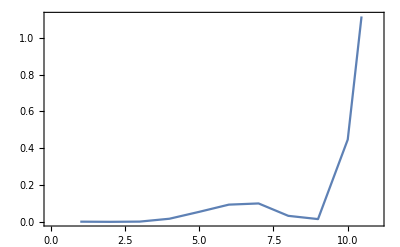

```mathematica
doubleGEMulti=ListPlot[ge,Joined->True,Frame->True]
```

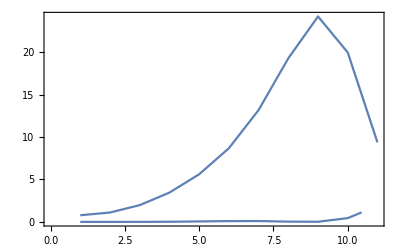

```mathematica
Show[doubleGESingle,doubleGEMulti]
```

## Other data

### Simple pendulum, large amplitude (1DOF, NL)

```mathematica
vars={x1};
eq={m1 x1''[t]==-k1 Sin[ x1[t]]};
params={m1->0.5,k1->2};
init={x1[0]==1.9 π/2,x1'[0]==0};
tTrain=10;
tMax=30;
tStep=0.1;
```

```mathematica
sol=NDSolve[Join[eq,init]/.params,vars,{t,0,tMax}];
```

```mathematica
p=dataFromSol[vars,sol,tTrain,tStep];
```

```mathematica
nd=NotebookDirectory[];
Export[nd<>"../data/mma_pendulum_large.csv",Transpose[{x1,x1d}/.p]];
```